# Quantum Mechanics

## Normalization and Probabilities

## Relative Statistics

Expectation value ( μ ): ⟨ x^k ⟩ = ∫ ψ^*x^k ψ dx

Standard Deviation ( σ ): σ_x =  √(⟨x^2⟩-⟨x⟩^2)

## Patterns

```mathematica
(* complex conjugate *)
```

```mathematica
SuperStar[φ_]:= φ/. Complex[u_,  v_]-> Complex[u, -v]
```

```mathematica
(* inner produt with optional operator and bounds *)
```

```mathematica
InnerProduct[⟨φ_,k_: 1, ψ_⟩, lower_:-Infinity ,  upper_:  Infinity]:= Integrate[SuperStar[φ] k ψ, {x, lower, upper}]
```

```mathematica
(* momentum operator *)
```

```mathematica
p̂[k_, var_] :=  (ℏ/I)^k D[#, {var,k}]&;(* 'I': complex, '#': derivative of var with respect to k*)
```

```mathematica
p̂[1, x]
```

```mathematica
(ℏ/ⅈ)^1 D[#1, {x,1}]& (* implies needs to be fead another function*)
```

```mathematica
p̂[1,x]@ψ[x]
```

-ⅈ ℏ ψ'[x]

## Examples

### Time Independent Wave Function

0		   x < 0
												ψ( x ) = { A x^2 (x-c)^2	0 ≤ x ≤ c
															0		   c < x

Determine normalization constant  “A”

Evaluate ⟨ x ⟩, ⟨ x^2 ⟩ and σ_x

Evaluate ⟨  p ⟩, ⟨ p^2 ⟩ and σ_p

Compute σ_x, σ_p

```mathematica
$Line = 0;
```

```mathematica
(* define wave function *)
```

```mathematica
ψ[x_ /; x < 0] := 0
ψ[x_] := A x^2 (x-c)^2
```

```mathematica
DownValues@ψ
```

{HoldPattern[ψ[x_/;x<0]]:>0,HoldPattern[ψ[x_]]:>A x^2 (x-c)^2}

```mathematica
(*  solve for normalization constant and update DownValue*)
```

```mathematica
Solve[InnerProduct[⟨ψ[x],  ψ[x] ⟩, 0, c ]== 1, A] [[2,1]]
```

A→(3 √70)/c^(9/2)

```mathematica
ψ[x_] = ψ[x]/. %; (* replace A with the previously computed output*)
```

```mathematica
DownValues@ψ
```

{HoldPattern[ψ[x_/;x<0]]:>0,HoldPattern[ψ[x_]]:>(3 √70 x^2 (-c+x)^2)/c^(9/2)}

```mathematica
(* show that the correct constant has been determined *)
```

```mathematica
InnerProduct[⟨ψ[x], ψ[x]⟩, 0, c] ==1
```

```mathematica
True  (*  correct normalization constant found *)
```

```mathematica
(* Evaluating ⟨x⟩, ⟨x^2⟩, Subscript[σ, x] *)
```

```mathematica
{#, #2,√(#2- #^2)}&@@(InnerProduct[⟨ψ[x], #, ψ[x]⟩, 0, c] &/@ {x, x^2})
```

{c/2,(3 c^2)/11,(√(c^2))/(2 √11)}

```mathematica
(* Evaluating ⟨p⟩, ⟨p^2⟩, Subscript[σ, p] *)
```

```mathematica
{#, #2,√(#2- #^2)}&@@(InnerProduct[⟨ψ[x],p̂[#, x]@ ψ[x]⟩, 0, c] &/@ {1,2})
```

{0,(12 ℏ^2)/c^2,2 √3 √(ℏ^2/c^2)}

```mathematica
(* Subscript[σ, x] Subscript[σ, p]> ℏ/2 *)
```

```mathematica
Out[10][[3]]Out[14][[3]]
```

√(3/11) √(c^2) √(ℏ^2/c^2)

```mathematica
unc = %
Assuming[c > 0 && ℏ > 0, Refine @(unc  > ℏ/2)]
```

√(3/11) √(c^2) √(ℏ^2/c^2)

True

### Time dependent Wave Function

Determine the normalization constant ‘n’

Is the probability of finding the particle in the interval (L, ∞) and t = 0 different from the probability at t = 10?

What is the probability of finding the particle in the interval ( ⟨ x ⟩ - σ_x, ⟨ x ⟩ + σ_x )?

```mathematica
(*  Set Global assumption *)
```

```mathematica
$Assumptions = L ∈ Reals && L > 0;
```

```mathematica
(* Defining the wave function *)
```

```mathematica
Ψ[x_, t_] :=  n Exp[-(Abs@x)/L- (ene I)/ℏ t]
```

```mathematica
DownValues@Ψ
```

{HoldPattern[Ψ[x_,t_]]:>n Exp[-Abs[x]/L-((ene ⅈ) t)/ℏ]}

```mathematica
(* Normalization coefficient *)
```

```mathematica
Solve[InnerProduct[⟨Ψ[x, t], Ψ[x, t]⟩]==1, n][[2,1]]
Ψ[x_, t_] = Ψ[x, t] /. %;  (* find pattern {Ψ[x, t]} replace {/.} 'n' with the previous output {%} *)
```

n→ⅇ^((ⅈ ene t)/ℏ)/(√L)

```mathematica
DownValues@Ψ
```

```mathematica
{HoldPattern[Ψ[x_,t_]]:>ⅇ^(-Abs[x]/L)/(√L)}
```

```mathematica
(* inner product over the specified interval  *)
```

```mathematica
{#, N@#}&@InnerProduct[⟨Ψ[x, t], Ψ[x, t]⟩, L, Infinity] (* {#, N@#} -> symbolic_value, numeric_value; & end of function, @-> affix *)
```

{1/(2 ⅇ^2),0.0676676}

```mathematica
(* <x>,  <x^2>, Subscript[σ, x]*)
```

```mathematica
{lower, upper} = {# - #3, # + #3}&@@{#, #2, √(#2 - #^2)}&@@(InnerProduct[⟨Ψ[x, t],#, Ψ[x, t]⟩]&/@ {x, x^2} )
```

{-(√(L^2))/(√2),(√(L^2))/(√2)}

```mathematica
{#, N@#}&@InnerProduct[⟨Ψ[x, t], Ψ[x, t]⟩, lower, upper]
```

{ⅇ^(-√2) (-1+ⅇ^(√2)),0.756883}

```mathematica
(* Potting *)
```

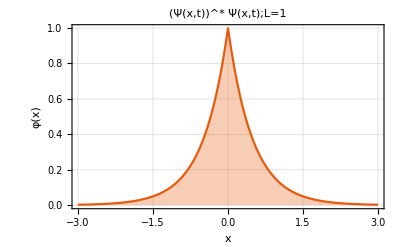

```mathematica
Plot[Evaluate[SuperStar[Ψ[x, t]] Ψ[x, t] /.  L-> 1.], {x, -3., 3.},
Filling -> Axis,
GridLines -> Automatic,
GridLines -> Automatic,
GridLinesStyle -> Directive[Dashed, GrayLevel[0.8]],
FrameLabel -> {"x", "φ(x)"},
PlotLabel -> HoldForm[SuperStar[Ψ[x, t]] Ψ[x, t]; L=1],
PlotTheme -> "Scientific"]
```